```mathematica
t=Tuples[{0,1},10];
```

```mathematica
t//Dimensions
```

{1024,10}

```mathematica
Flatten[t,3]//Dimensions
```

{10240}

```mathematica
t[[1025]]
```

Part::partw: Part 1025 of {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 1}, « 36 », {0, 0, 0, 0, 1, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 1, 0, 1}, {0, 0, 0, 0, 1, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 1, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0, 0, 0, 1}, « 974 »} does not exist.

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,1,0},«1010»,{1,1,1,1,1,1,1,0,0,1},{1,1,1,1,1,1,1,0,1,0},{1,1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1}}⟦1025⟧

```mathematica
t//Dimensions
```

{1024,10}

```mathematica
Export["Tuples10.txt",t]
```

Tuples10.txt

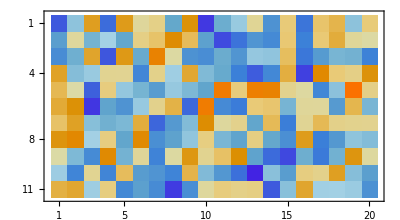

```mathematica
PartitionNest[{w_},n_]:={Transpose@Partition[w,n+1]};
PartitionNest[{w_,rest__},n_]:=Prepend[PartitionNest[{rest},Length[w]/(n+1)],Transpose@Partition[w,n+1]];
lists=Import["~/weightsparity2.tsv"];
wp1=PartitionNest[lists,10];
MatrixPlot[#,ImageSize->400]&/@wp1
```

```mathematica
wp1//Dimensions
```

{1,9,20}

```mathematica
{0,0}/.weightrule
```

0.5

```mathematica
weightrule={{0,0}->0.5,{1,1}->0.5,{0,1}->1,{1,0}->0};
```

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
```

```mathematica
weight=0;
Do[

colorstest={{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1}};
data11=Append[2*#-1,1]&/@colorstest;
up1=SampleHidden[wp1[[1]]][#]&/@data11;
down1=SampleVisible[wp1[[1]]][#]&/@up1;
Final=Most[#1]&/@Map[((#+1)/2)&,down1];
{a,b}={Final[[1,-2;;-1]],Final[[2,-2;;-1]]}/.weightrule;
weight=weight+a+b;

,{loop,50}];
weight/100
```

0.425